```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-((2857-(5033/9)Nf+(325/27) Nf^2)/128); (*for Nc=3 only*)
β3[Nf_]=((-1)/256)((149753/6+3564 Zeta[3])-(1078361/162+(6508/27) Zeta[3])Nf+(50065/162+(6472/81)Zeta[3])Nf^2+(1093/729) Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=(1/16)(202/3-(20/9)Nf);(*for Nc=3 only*)
γ2[Nf_]=(1/64)(1249+(-(2216/27)-(160/3) Zeta[3])Nf-(140/81) Nf^2);(*for Nc=3 only*)
γ3[Nf_]=(1/256)(4603055/162+(135680/27) Zeta[3]-8800Zeta[5]+(-(91723/27)-(34192/9) Zeta[3]+880 Zeta[4]+(18400/9)Zeta[5])Nf+(5242/243+(800/9) Zeta[3]-(160/3)Zeta[4])Nf^2+(-(332/243)+(64/27) Zeta[3])Nf^3);

b0[Nf_]=-((8β0[Nf])/(2(4π)^2));
b1[Nf_]=-((32 β1[Nf])/(2(4π)^2));

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=(-1)/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-( β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+(1/(β0[Nf]^7 t^4))( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Potentials

```mathematica
kfinal={0.6802525363662164,-0.31465604392609736};(*100k run*)
kfinalu={0.9017845365143496,-0.3669424499609976};
kfinall={0.4587205362180833,-0.26236963789119705};
αcont=SetPrecision[{0.5146004500017507,0.002579680095957094},20];(*10k run*)
σcont=SetPrecision[{0.16904257426266697,0.0009046347484072015},20];
ccont=SetPrecision[{-0.15782092474161866,0.0024785523617348124},20];
```

### Define required functions

```mathematica
Πpar[θ_,mD_,u_]:=mD^2/2((2-2 u^2-u^4 Cos[θ]^2 Sin[θ]^2)/((1-u^2 Sin[θ]^2)^2)-((2+u^2 Sin[θ]^2)(1-u^2)u Cos[θ])/(2(1-u^2 Sin[θ]^2)^(5/2))Log[(u Cos[θ]+√(1-u^2 Sin[θ]^2))/(u Cos[θ]-√(1-u^2 Sin[θ]^2))]);
ReVcpp[r_,mD_,u_,α_,c_]:=Re[c-α/r+α  NIntegrate[Sin[θ] √Πpar[θ,mD,u] Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20]];
ReVspp[r_,mD_,u_,σ_]:=Re[σ NIntegrate[Sin[θ] 1/(√Πpar[θ,mD,u])Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20]];
ReVsp[r_,mD_,u_,σ_]:=σ NIntegrate[Sin[θ] 1/Re[√Πpar[θ,mD,u]] Exp[-Re[√Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20];
ReVcp[r_,mD_,u_,α_,c_]:=c-α mD-α/r+α NIntegrate[Sin[θ] √Re[Πpar[θ,mD,u]] Exp[-√Re[Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20];
ϵRep[r_,mD_,u_]:=1/(4π)(2/r NIntegrate[Cos[θ]Sin[θ]Re[Πpar[θ,mD,u]]Exp[-√Re[Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2}]-NIntegrate[Cos[θ]^2 Sin[θ] Re[Πpar[θ,mD,u]]^(3/2)Exp[-√Re[Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2}]);
ϵRepp[r_,mD_,u_]:=Re[1/(4π)(2/r NIntegrate[Cos[θ]Sin[θ]Πpar[θ,mD,u]Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2}]-NIntegrate[Cos[θ]^2 Sin[θ] Πpar[θ,mD,u]^(3/2)Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2}])];
ReVsTab[mD1_,u1_,σ1_]:=Block[{u=u1,mD=mD1,σ=σ1,tab0,tab1,temp,inter0,inter1,inter2,tab2},tab0=ParallelTable[{r,-4π σ r^2 ϵRep[r,mD,u]},{r,10^-10,200,1/100}];
inter0=Interpolation[tab0];
inter1[r_]:=NIntegrate[inter0[r1],{r1,0,r}];
temp=inter1[200];
tab1=ParallelTable[{r,inter1[r]-temp},{r,0,200,1/100}];
inter1=Interpolation[tab1];
inter2[r_]:=NIntegrate[inter1[r1],{r1,0,r}];
tab2=ParallelTable[{r,inter2[r]},{r,0,200,1/100}];
Export["mathematica/vel_pot/ReVsu"<>ToString[Round[100 u]]<>".dat",tab2];
Return[Interpolation[tab2]]];
ImVcp[r_,mD_,u_,α_,T_]:=2 α T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,mD,u]-Conjugate[Πpar[x,mD,u]])(Sinh[√Πpar[x,mD,u] r Cos[x]]SinhIntegral[√Πpar[x,mD,u] r Cos[x]]-Cosh[√Πpar[x,mD,u] r Cos[x]]CoshIntegral[√Πpar[x,mD,u] r Cos[x]]-Sinh[√Conjugate[Πpar[x,mD,u]] r Cos[x]]SinhIntegral[√Conjugate[Πpar[x,mD,u]] r Cos[x]]+Cosh[√Conjugate[Πpar[x,mD,u]] r Cos[x]]CoshIntegral[√Conjugate[Πpar[x,mD,u]] r Cos[x]]),{x,0,π/2},MaxRecursion->20];
ϵImp[r_,mD_,u_,T_]:=Re[1/(2π)T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,mD,u]-Conjugate[Πpar[x,mD,u]])1/r Cos[x] (2 √Conjugate[Πpar[x,mD,u]] (CoshIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]] Sinh[r √Conjugate[Πpar[x,mD,u]] Cos[x]]-Cosh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]])+r Conjugate[Πpar[x,mD,u]] Cos[x] (Cosh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] CoshIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]]-Sinh[r √Conjugate[Πpar[x,mD,u]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,mD,u]] Cos[x]])+√Πpar[x,mD,u] (-CoshIntegral[r Cos[x] √Πpar[x,mD,u]] (r Cos[x] Cosh[r Cos[x] √Πpar[x,mD,u]] √Πpar[x,mD,u]+2 Sinh[r Cos[x] √Πpar[x,mD,u]])+(2 Cosh[r Cos[x] √Πpar[x,mD,u]]+r Cos[x] √Πpar[x,mD,u] Sinh[r Cos[x] √Πpar[x,mD,u]]) SinhIntegral[r Cos[x] √Πpar[x,mD,u]])),{x,0,π/2},WorkingPrecision->20]];
ImVsTab[mD1_,u1_,σ1_,T1_]:=Block[{u=u1,mD=mD1,σ=σ1,T=T1,tab0,tab1,inter0,inter1,inter2,temp,tab2},tab0=ParallelTable[{r,4π σ r^2 ϵImp[r,mD,u,T]},{r,10^-10,50,1/100}];
inter0=Interpolation[tab0];
inter1[r_]:=NIntegrate[inter0[r1],{r1,0,r}];
temp=inter1[0];
tab1=ParallelTable[{r,inter1[r]-temp},{r,10^-10,50,1/100}];
inter1=Interpolation[tab1];
inter2[r_]:=NIntegrate[inter1[r1],{r1,0,r}];
tab2=ParallelTable[{r,inter2[r]},{r,0,50,1/100}];
Export["mathematica/vel_pot/ImVsu"<>ToString[Round[100 u]]<>".dat",tab2];
Return[Interpolation[tab2]]];
```

```mathematica
mDcalmu[T_,μ_,c_,d_]:=SetPrecision[Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(μ/3)^2/T^2]g4[2π √(T^2+μ^2/π^2)]T+1/(4π)Nc g4[2π √(T^2+μ^2/π^2)]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π √(T^2+μ^2/π^2)]]+c g4[2π √(T^2+μ^2/π^2)]^2 T+d g4[2π √(T^2+μ^2/π^2)]^3 T ],20];
```

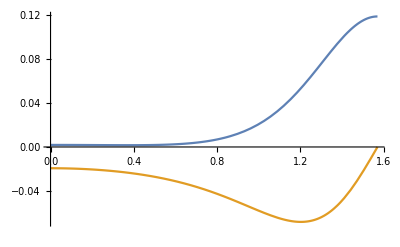

```mathematica
Plot[{Re[Πpar[x,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],0.8]],Im[Πpar[x,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],0.8]]},{x,0,π/2}]
```

```mathematica
Block[{u=8/10,mD=1/2,σ=σcont[[1]]},tab0=Table[{r,-4π σ r^2 ϵRep[r,mD,u]},{r,10^-10,100,1/10}]];
```

```mathematica
Clear[inter0]
```

```mathematica
inter0=Interpolation[tab0];
```

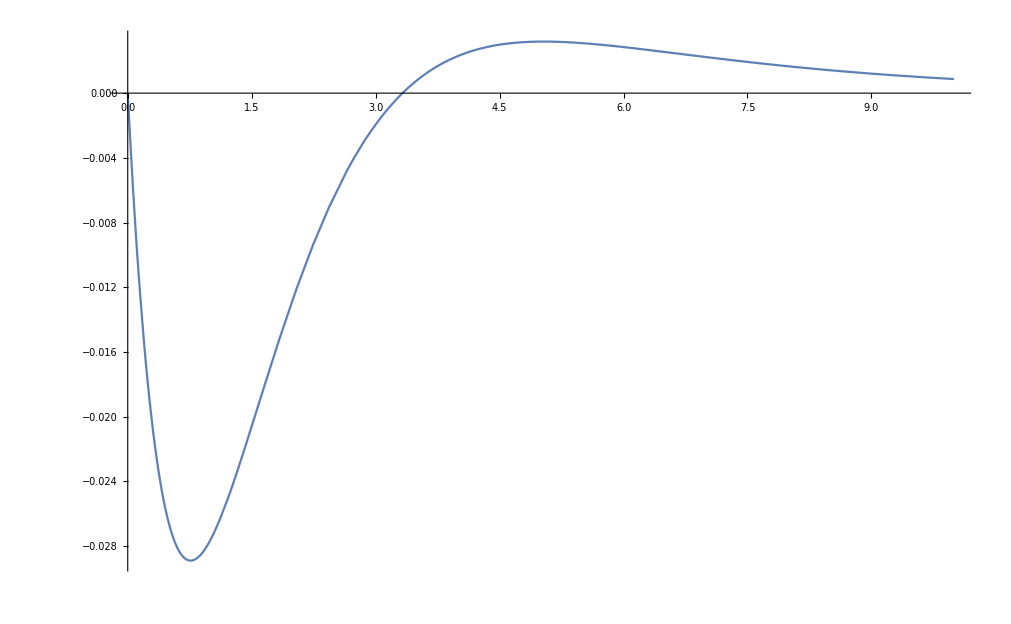

```mathematica
Plot[inter0[x/0.197],{x,0,10},PlotRange->All]
```

```mathematica
Block[{u=8/10,mD=1/2,σ=σcont[[1]]},tab00=Table[{r,-4π σ r^2 ϵRepp[r,mD,u]},{r,10^-10,100,1/10}]];
```

```mathematica
inter00=Interpolation[tab00];
```

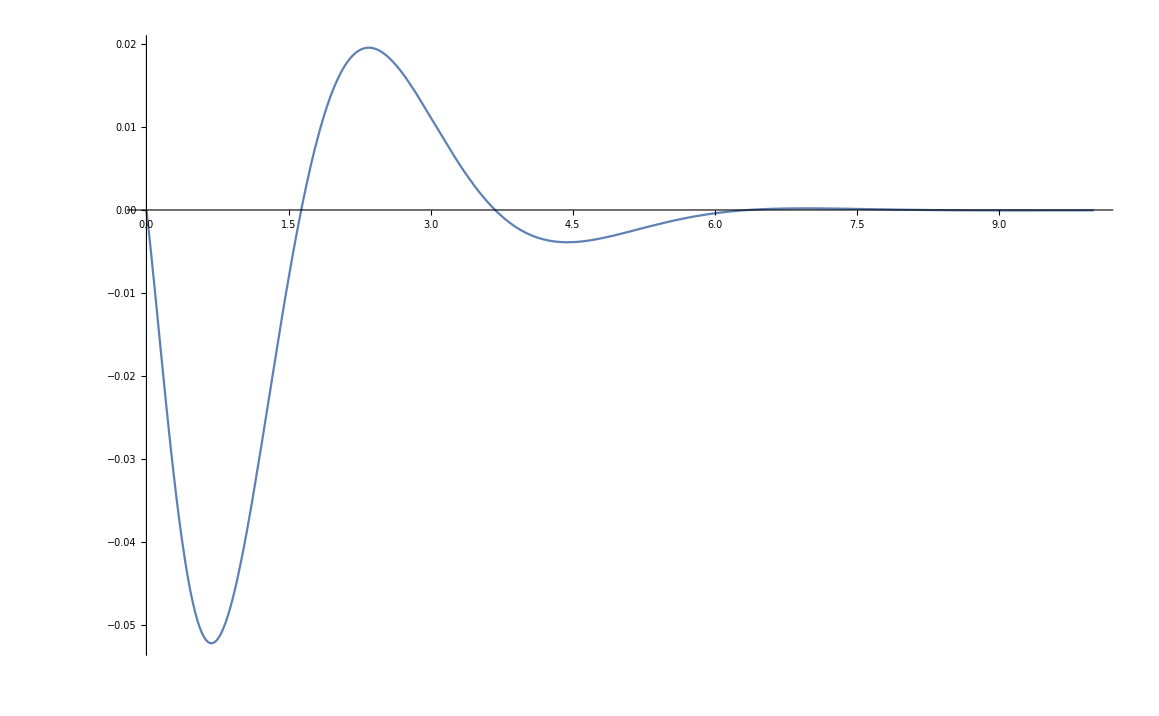

```mathematica
Plot[inter00[x/0.197],{x,0,10},PlotRange->All]
```

```mathematica
Clear[inter1]
```

```mathematica
inter1[r_]:=NIntegrate[inter0[r1],{r1,0,r}];
```

```mathematica
temp=inter1[100]
```

-0.170325

```mathematica
tab1=ParallelTable[{r,inter1[r]-temp},{r,0,100,1/10}];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
Clear[inter1]
```

```mathematica
inter1=Interpolation[tab1];
```

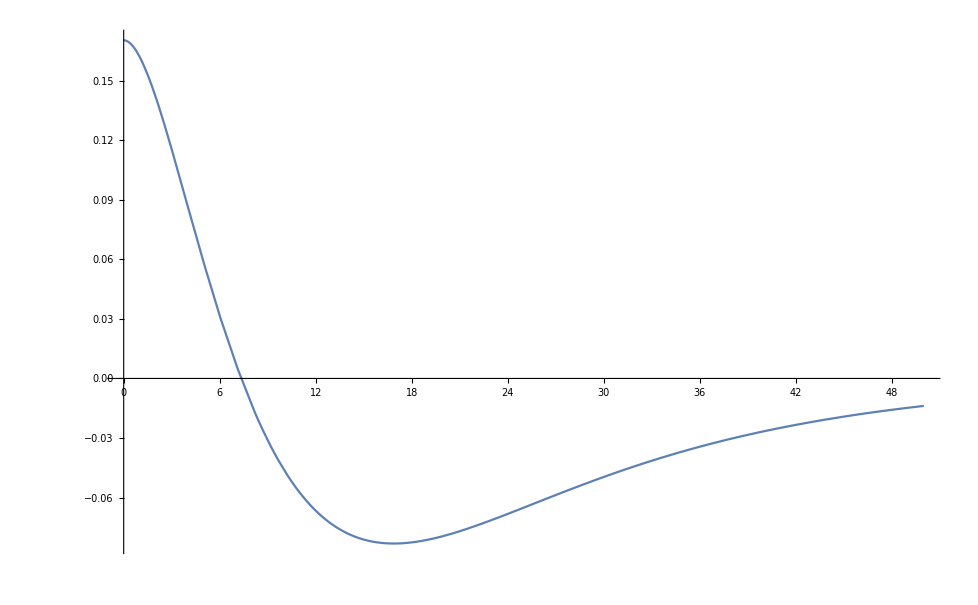

```mathematica
Plot[inter1[x],{x,0,50},PlotRange->All]
```

```mathematica
Clear[inter10]
```

```mathematica
inter10[r_]:=NIntegrate[inter00[r1],{r1,0,r}];
```

```mathematica
temp0=inter10[100]
```

-0.168868

```mathematica
tab10=ParallelTable[{r,inter10[r]-temp0},{r,0,100,1/10}];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
Clear[inter10]
```

```mathematica
inter10=Interpolation[tab10];
```

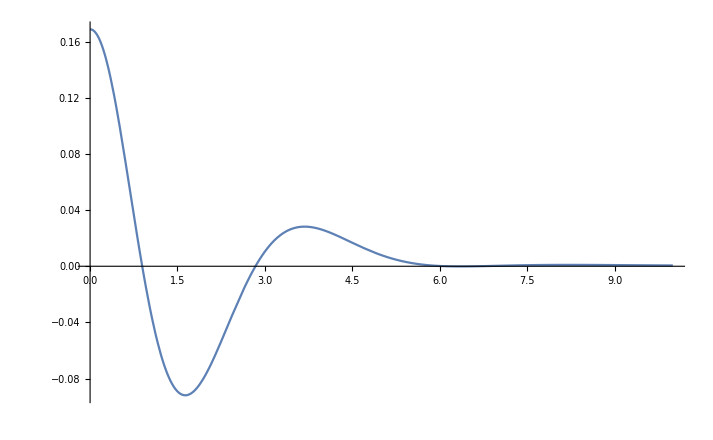

```mathematica
Plot[inter10[x/0.197],{x,0,10},PlotRange->All]
```

```mathematica
Clear[tab2,res]
```

```mathematica
inter2[r_]:=NIntegrate[inter1[r1],{r1,0,r}];
tab2=ParallelTable[{r,inter2[r]},{r,0,100,1/10}];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
res=Interpolation[tab2];
```

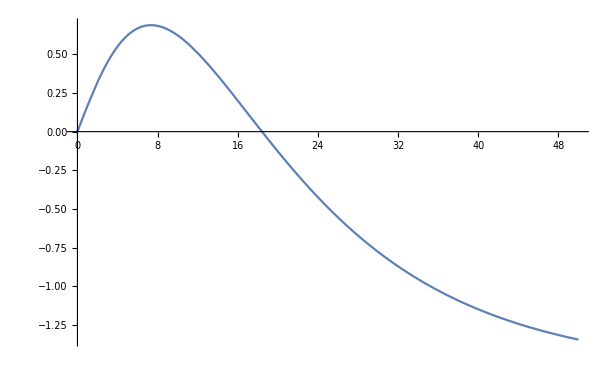

```mathematica
Plot[res[x],{x,0,50},PlotRange->All]
```

```mathematica
ReVs[r_,mD_,σ_]:=(2 σ)/mD-(ⅇ^(-mD r) (2+mD r) σ)/mD;
```

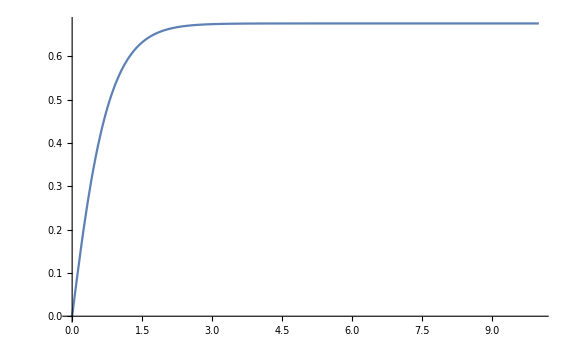

```mathematica
Plot[ReVs[r/0.197,1/2,σcont[[1]]],{r,0,10},PlotRange->All]
```

### Plot potentials

```mathematica
ReVcp[200,2/10,8/10,αcont[[1]],ccont[[1]]]
```

-0.2607306396156355594

```mathematica
ImVcp[100,2/10,8/10,αcont[[1]],155/1000]
```

-0.0000403978+3.74205×10^-12 ⅈ

```mathematica
ϵRep[200,2/10,8/10]
```

-6.46849×10^-10

```mathematica
ReVsTab[2/10,1/10,σcont[[1]]];
ReVsTab[2/10,2/10,σcont[[1]]];
ReVsTab[2/10,3/10,σcont[[1]]];
ReVsTab[2/10,4/10,σcont[[1]]];
ReVsTab[2/10,5/10,σcont[[1]]];
ReVsTab[2/10,6/10,σcont[[1]]];
ReVsTab[2/10,7/10,σcont[[1]]];
ReVsTab[2/10,8/10,σcont[[1]]];
```

```mathematica
ImVsTab[2/10,1/10,σcont[[1]],155/1000];
ImVsTab[2/10,2/10,σcont[[1]],155/1000];
ImVsTab[2/10,3/10,σcont[[1]],155/1000];
ImVsTab[2/10,4/10,σcont[[1]],155/1000];
ImVsTab[2/10,5/10,σcont[[1]],155/1000];
ImVsTab[2/10,6/10,σcont[[1]],155/1000];
ImVsTab[2/10,7/10,σcont[[1]],155/1000];
ImVsTab[2/10,8/10,σcont[[1]],155/1000];
```

```mathematica
temp=ImVcp[10^-10,2/10,3/10,αcont[[1]],155/1000];
temp1=ParallelTable[{r,ImVcp[r,2/10,3/10,αcont[[1]],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu30.dat",temp1];
```

```mathematica
temp=ImVcp[10^-10,2/10,4/10,αcont[[1]],155/1000];
temp1=ParallelTable[{r,ImVcp[r,2/10,4/10,αcont[[1]],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu40.dat",temp1];
```

```mathematica
temp=ImVcp[10^-10,2/10,5/10,αcont[[1]],155/1000];
temp1=ParallelTable[{r,ImVcp[r,2/10,5/10,αcont[[1]],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu50.dat",temp1];
```

```mathematica
temp=ImVcp[10^-10,2/10,6/10,αcont[[1]],155/1000];
temp1=ParallelTable[{r,ImVcp[r,2/10,6/10,αcont[[1]],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu60.dat",temp1];
```

```mathematica
temp=ImVcp[10^-10,2/10,7/10,αcont[[1]],155/1000];
temp1=ParallelTable[{r,ImVcp[r,2/10,7/10,αcont[[1]],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu70.dat",temp1];
```

```mathematica
temp=ImVcp[10^-10,2/10,8/10,αcont[[1]],155/1000];
temp1=ParallelTable[{r,ImVcp[r,2/10,8/10,αcont[[1]],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu80.dat",temp1];
```

```mathematica
Export["mathematica/vel_pot/ReVcu10.dat",ParallelTable[{r,ReVcp[r,2/10,1/10,αcont[[1]],ccont[[1]]]},{r,1/1000,200,1/100}]];
Export["mathematica/vel_pot/ReVcu20.dat",ParallelTable[{r,ReVcp[r,2/10,2/10,αcont[[1]],ccont[[1]]]},{r,1/1000,200,1/100}]];
Export["mathematica/vel_pot/ReVcu30.dat",ParallelTable[{r,ReVcp[r,2/10,3/10,αcont[[1]],ccont[[1]]]},{r,1/1000,200,1/100}]];
Export["mathematica/vel_pot/ReVcu40.dat",ParallelTable[{r,ReVcp[r,2/10,4/10,αcont[[1]],ccont[[1]]]},{r,1/1000,200,1/100}]];
Export["mathematica/vel_pot/ReVcu50.dat",ParallelTable[{r,ReVcp[r,2/10,5/10,αcont[[1]],ccont[[1]]]},{r,1/1000,200,1/100}]];
Export["mathematica/vel_pot/ReVcu60.dat",ParallelTable[{r,ReVcp[r,2/10,6/10,αcont[[1]],ccont[[1]]]},{r,1/1000,200,1/100}]];
Export["mathematica/vel_pot/ReVcu70.dat",ParallelTable[{r,ReVcp[r,2/10,7/10,αcont[[1]],ccont[[1]]]},{r,1/1000,200,1/100}]];
Export["mathematica/vel_pot/ReVcu80.dat",ParallelTable[{r,ReVcp[r,2/10,8/10,αcont[[1]],ccont[[1]]]},{r,1/1000,200,1/100}]];
```

```mathematica
ReVsTab[SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],20],1/100,σcont[[1]]];
ImVsTab[SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],20],1/100,σcont[[1]],155/1000];
temp=ImVcp[10^-10,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],20],1/100,αcont[[1]],155/1000];
temp1=ParallelTable[{r,ImVcp[r,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],20],1/100,αcont[[1]],155/1000]-temp},{r,1/1000,60,1/100}];
Export["mathematica/vel_pot/ImVcu01.dat",temp1];
Export["mathematica/vel_pot/ReVcu02.dat",ParallelTable[{r,ReVcp[r,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],20],1/100,αcont[[1]],ccont[[1]]]},{r,1/1000,200,1/100}]];
```

## Plot potentials

### mD = 0.2 GeV, T = 0.155 GeV

```mathematica
ReVsu10=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu10.dat"]]];
ReVsu20=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu20.dat"]]];
ReVsu30=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu30.dat"]]];
ReVsu40=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu40.dat"]]];
ReVsu50=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu50.dat"]]];
ReVsu60=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu60.dat"]]];
ReVsu70=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu70.dat"]]];
ReVsu80=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVsu80.dat"]]];
```

```mathematica
ReVcu10=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu10.dat"]]];
ReVcu20=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu20.dat"]]];
ReVcu30=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu30.dat"]]];
ReVcu40=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu40.dat"]]];
ReVcu50=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu50.dat"]]];
ReVcu60=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu60.dat"]]];
ReVcu70=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu70.dat"]]];
ReVcu80=Interpolation[ToExpression[Import["mathematica/vel_pot/ReVcu80.dat"]]];
```

```mathematica
ImVcu10=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu10.dat"]]];
ImVcu20=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu20.dat"]]];
ImVcu30=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu30.dat"]]];
ImVcu40=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu40.dat"]]];
ImVcu50=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu50.dat"]]];
ImVcu60=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu60.dat"]]];
ImVcu70=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu70.dat"]]];
ImVcu80=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVcu80.dat"]]];
```

```mathematica
ImVsu10=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu10.dat"]]];
ImVsu20=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu20.dat"]]];
ImVsu30=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu30.dat"]]];
ImVsu40=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu40.dat"]]];
ImVsu50=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu50.dat"]]];
ImVsu60=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu60.dat"]]];
ImVsu70=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu70.dat"]]];
ImVsu80=Interpolation[ToExpression[Import["mathematica/vel_pot/ImVsu80.dat"]]];
```

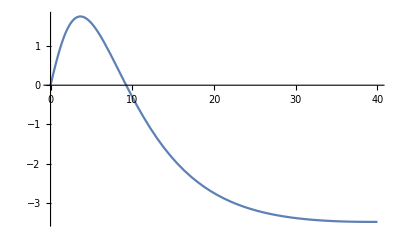

```mathematica
Plot[ReVsu80[r/0.197],{r,0,40},PlotRange->All]
```

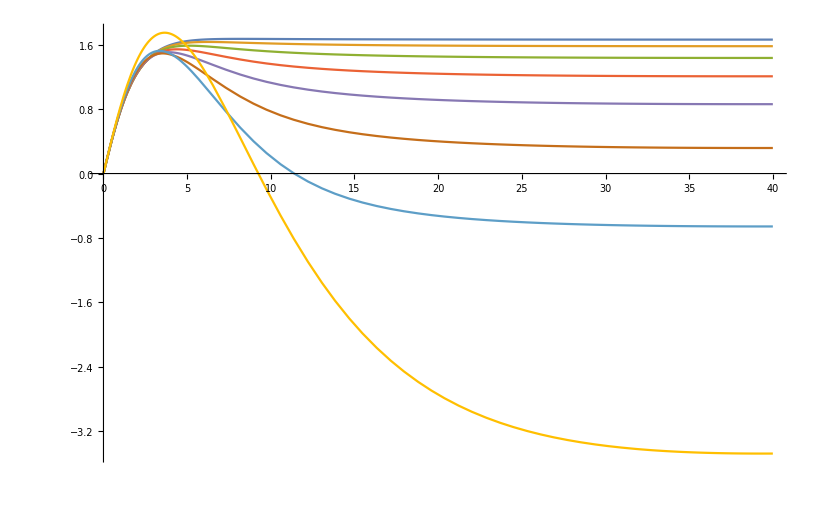

```mathematica
Plot[{ReVsu10[r/0.197],ReVsu20[r/0.197],ReVsu30[r/0.197],ReVsu40[r/0.197],ReVsu50[r/0.197],ReVsu60[r/0.197],ReVsu70[r/0.197],ReVsu80[r/0.197]},{r,0,40},PlotRange->All]
```

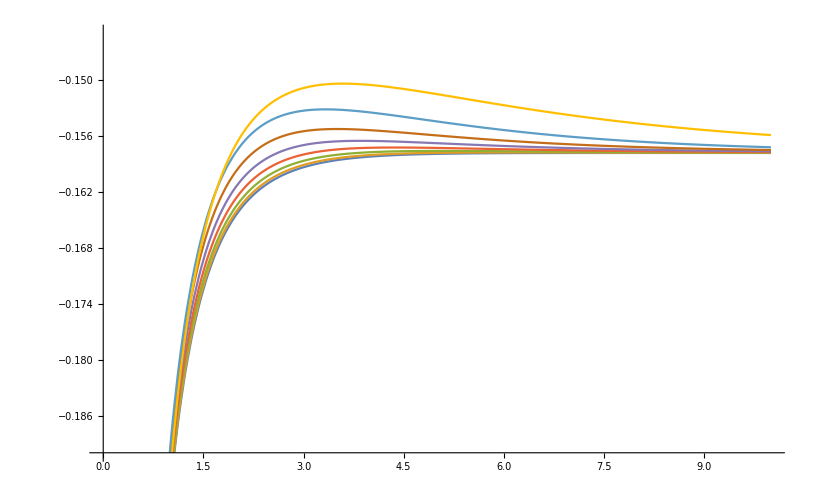

```mathematica
Plot[{ReVcu10[r/0.197],ReVcu20[r/0.197],ReVcu30[r/0.197],ReVcu40[r/0.197],ReVcu50[r/0.197],ReVcu60[r/0.197],ReVcu70[r/0.197],ReVcu80[r/0.197]},{r,0,10},PlotRange->{-0.19,-0.145}]
```

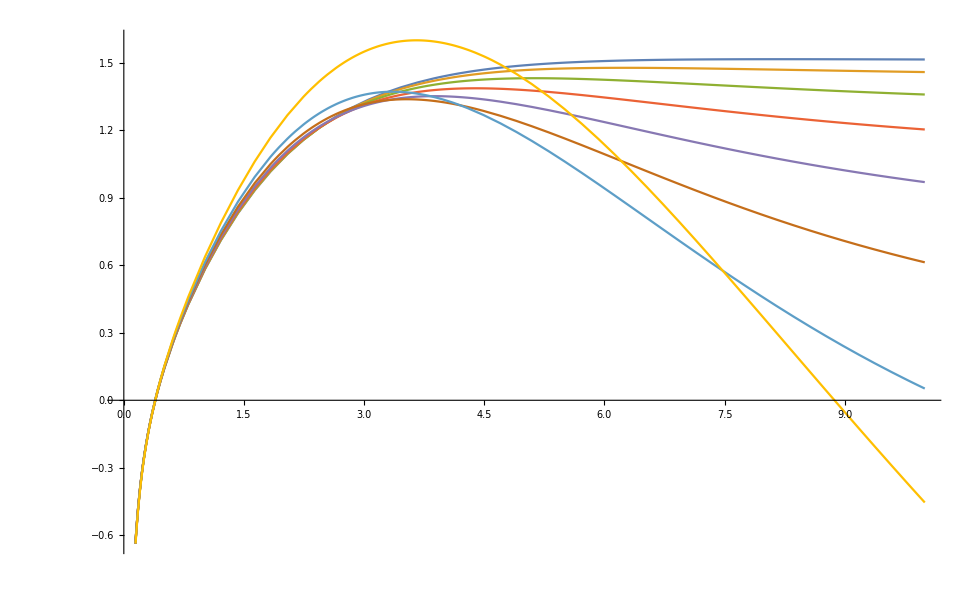

```mathematica
Plot[{ReVsu10[r/0.197]+ReVcu10[r/0.197],ReVcu20[r/0.197]+ReVsu20[r/0.197],ReVsu30[r/0.197]+ReVcu30[r/0.197],ReVsu40[r/0.197]+ReVcu40[r/0.197],ReVsu50[r/0.197]+ReVcu50[r/0.197],ReVsu60[r/0.197]+ReVcu60[r/0.197],ReVsu70[r/0.197]+ReVcu70[r/0.197],ReVsu80[r/0.197]+ReVcu80[r/0.197]},{r,0,10}]
```

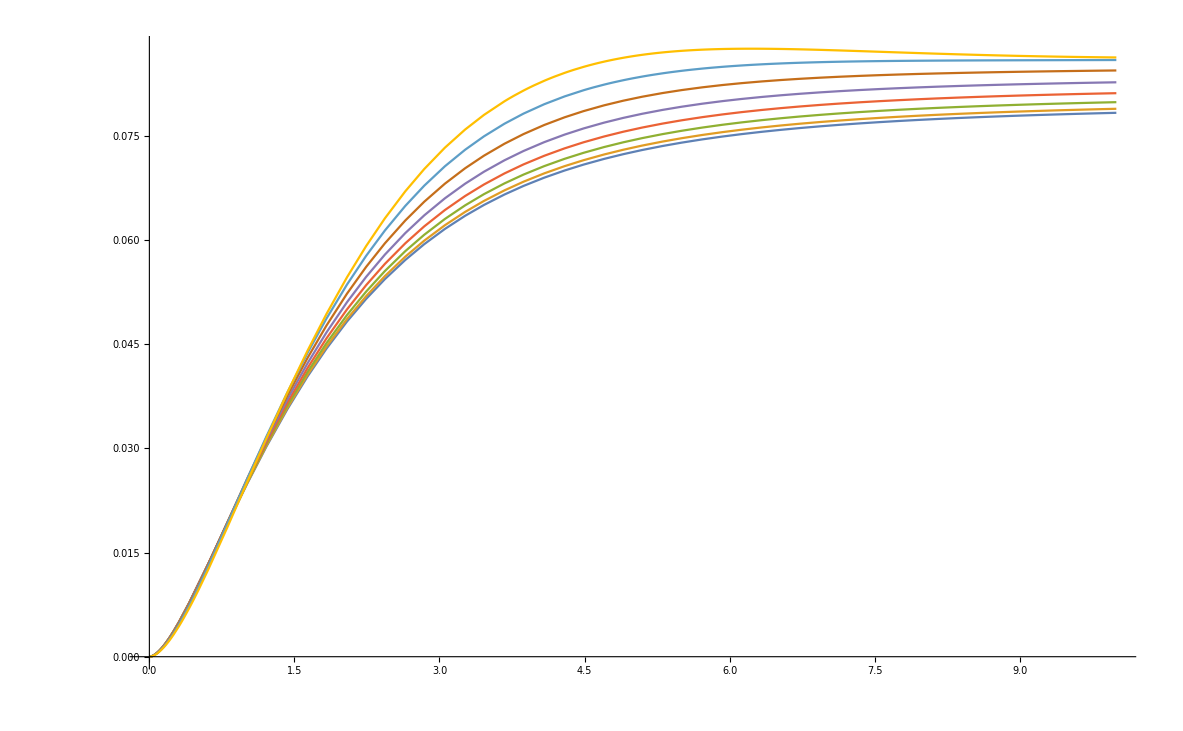

```mathematica
Plot[{Re[ImVcu10[r/0.197]],Re[ImVcu20[r/0.197]],Re[ImVcu30[r/0.197]],Re[ImVcu40[r/0.197]],Re[ImVcu50[r/0.197]],Re[ImVcu60[r/0.197]],Re[ImVcu70[r/0.197]],Re[ImVcu80[r/0.197]]},{r,1/1000,10},PlotRange->All]
```

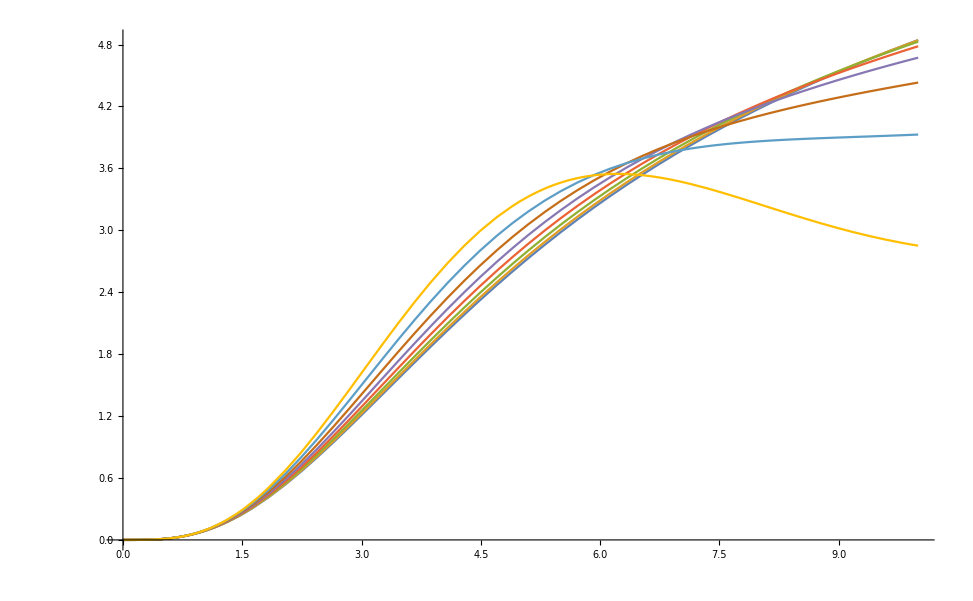

```mathematica
Plot[{ImVsu10[r/0.197],ImVsu20[r/0.197],ImVsu30[r/0.197],ImVsu40[r/0.197],ImVsu50[r/0.197],ImVsu60[r/0.197],ImVsu70[r/0.197],ImVsu80[r/0.197]},{r,0,10},PlotRange->All]
```

## Check paper results

```mathematica
ReVcu10pp=Interpolation[ParallelTable[{r,ReVcpp[r,1/2,1/10,αcont[[1]],ccont[[1]]]},{r,1/1000,50,1/100}]];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
ReVcu10p=Interpolation[ParallelTable[{r,ReVcp[r,1/2,1/10,αcont[[1]],ccont[[1]]]},{r,1/1000,50,1/100}]];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

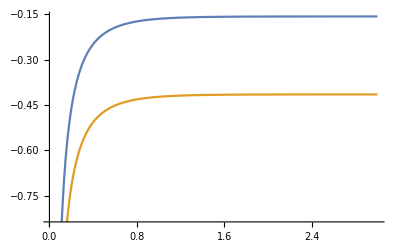

```mathematica
Plot[{ReVcu10pp[x/0.197],ReVcu10p[x/0.197]},{x,1/100,3}]
```

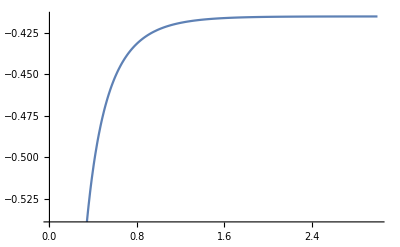

```mathematica
Plot[ReVcu10p[x/0.197],{x,1/100,3}]
```

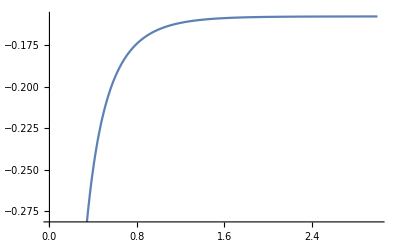

```mathematica
Plot[ReVcu10pp[x/0.197],{x,1/100,3}]
```

```mathematica
ReVsu10pp=Interpolation[ParallelTable[{r,ReVspp[r,1/2,1/20,σcont[[1]]]},{r,1/1000,50,1/100}]];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
ReVsu10p=Interpolation[ParallelTable[{r,ReVsp[r,1/2,1/20,σcont[[1]]]},{r,1/1000,50,1/100}]];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

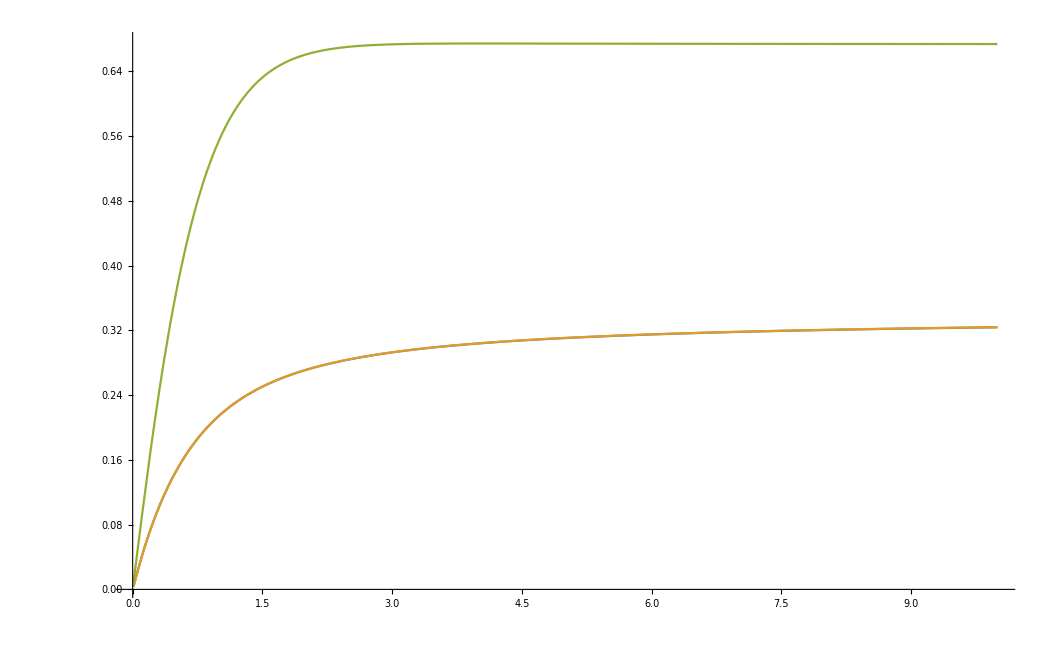

```mathematica
Plot[{-ReVsu10pp[x/0.197]+ReVsu10pp[1/100],-ReVsu10p[x/0.197]+ReVsu10p[1/100],res[x/0.197]},{x,1/100,10},PlotRange->All]
```

## Own real space permittivity

```mathematica
Limit[Assuming[{r∈Reals,r>0,x∈Reals,a∈Reals,a>0},Integrate[p^4/(p^2+f[x])Exp[ⅈ p r Cos[x]]Exp[-a p],{p,0,∞}]],a->0]//FullSimplify
```

ConditionalExpression[MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 Cos[x]^2 f[x]]/(2 √π (1/f[x])^(3/2)),Re[√f[x]]>0]

```mathematica
Limit[Assuming[{r∈Reals,r>0,x∈Reals,a∈Reals,a>0},Integrate[p^4/(p^2)Exp[ⅈ p r Cos[x]]Exp[-a p],{p,0,∞}]],a->0]//FullSimplify
```

-(2 ⅈ Sec[x]^3)/r^3

```mathematica
ϵRe[r_,mD_,u_]:=(2π)/(2π)^3 NIntegrate[Sin[θ] MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 Cos[θ]^2 Re[Πpar[θ,u,mD]]]/(2 √π (1/Re[Πpar[θ,u,mD]])^(3/2)),{θ,0,π},MaxRecursion->20];
```

```mathematica
ϵRe1[r_,mD_,u_]:=1/(4π) NIntegrate[Sin[θ] Re[Πpar[θ,u,mD]]^(3/2)Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}];
```

```mathematica
ϵRep2[r_,mD_,u_]:=-1/(4π r^2) NIntegrate[Sin[θ] Cos[θ]^2 Re[Πpar[θ,u,mD]]^(1/2)Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}];
```

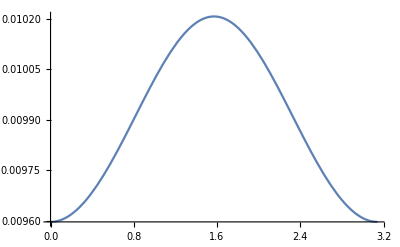

```mathematica
Plot[Re[Πpar[θ,0.01,0.2]]^(1/2),{θ,0,π}]
```

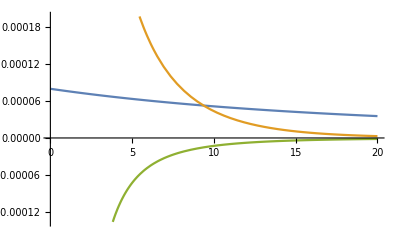

```mathematica
Block[{mD=0.2,u=0.1},Plot[{ϵRe1[r,mD,u],ϵRep[r,mD,u],ϵRep2[r,mD,u]},{r,1/100,20}]]
```

```mathematica
ϵu0[r_,mD_,T_]:=-(ⅇ^(-mD r) mD^2)/(4π r)-ⅈ T(mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/(4 π r);
```

```mathematica
ϵRe[10,0.2,1/100]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in θ near {θ} = {1.5708}. NIntegrate obtained 2.99697×10^-6+9.55411×10^12 ⅈ and 9.29332×10^12 for the integral and error estimates.

7.59141×10^-8+2.42009×10^11 ⅈ

```mathematica
Block[{r=10,mD=0.2},(2π)/(2π)^3 NIntegrate[Sin[θ] Re[MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 Cos[θ]^2 mD^2]]/(2 √π (1/mD^2)^(3/2)),{θ,0,π},MaxRecursion->20]]
```

0.000275231

```mathematica
ϵRe1[10,0.2,1/10000]
```

7.9579×10^-14

```mathematica
Block[{r=10,mD=0.2},1/(4π) NIntegrate[Sin[θ] mD^3 Exp[-mD r Cos[θ]],{θ,0,π/2}]]
```

0.000275231

```mathematica
1/(4π) Integrate[Sin[θ] mD^3 Exp[-mD r Cos[θ]],{θ,0,π/2}]
```

((1-ⅇ^(-mD r)) mD^2)/(4 π r)

```mathematica
ϵRep2[10,0.2,0.0]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
ϵRep[10,0.2,0.0]
```

0.0000430786

```mathematica
ϵu0[10,0.2,0]
```

-0.0000430786

```mathematica
Integrate[mD Sin[θ] Cos[θ]^2 Exp[- mD r Cos[θ]],{θ,0,π/2}]//FullSimplify
```

(ⅇ^(-mD r) (-2+2 ⅇ^(mD r)-mD r (2+mD r)))/(mD^2 r^3)

```mathematica
-1/(4 π r^2)(ⅇ^(-mD r) (-2+2 ⅇ^(mD r)-mD r (2+mD r)))/(mD^2 r^3)/.{mD->0.2,r->10}
```

-0.0000128646